## Invoice

Getting the data from the invoice.csv file (may take a few seconds)

We import the Data from the invoice.csv file,

Take the headers from the first row of the csv file

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) invoice

```mathematica
csv=Import[FileNameJoin[{NotebookDirectory[],"data_code","invoice.csv"}]];
headers=First[csv];
assoc=Association[Thread[headers->#]]&/@Rest[csv];
invoice=Dataset[assoc];
Clear[assoc]
```

Getting the data from the items.csv

We import the Data from the item.csv file,

Take the headers from the first row of the csv file and call it headersItem

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) item

```mathematica
csvItem=Import[FileNameJoin[{NotebookDirectory[],"data_code","item.csv"}]];
headersItem=First[csvItem];
assocItem=Association[Thread[headersItem->#]]&/@Rest[csvItem];
item=Dataset[assocItem];
Remove[assocItem]
```

Getting the data from the review.csv (put together using datMerger.nb)

We import the Data from the review.csv file,

Take the headers from the first row of the csv file and call it headersItem

build a list of associations(Key-Value datastructures) to be fed into a Dataset

Create a Dataset (like dataframe from pandas) item

```mathematica
csvReview=Import[FileNameJoin[{NotebookDirectory[],"reviews","review.csv"}]];
headersReview=First[csvReview];
assocReview=Association[Thread[headersReview->#]]&/@Rest[csvReview];
review=Dataset[assocReview];
Remove[assocReview]
```

Here we look at the lengths of the datasets

```mathematica
{Length[invoice],Length[item],Length[review]}
```

{930508,4166,50000}

and the names of the headers for each

```mathematica
headers
```

{Invoice_id,Date,Item_id,Vendor_id,Vendor_Name,Store_id,Store_Name,Address,City_Name,Zip_Code,County_id,County_Name,Bottles_Sold}

```mathematica
headersItem
```

{Item_id,Item_Description,Category,Pack,Bottle_Volume_ml,Bottle_Cost,Bottle_Retail_Price}

```mathematica
headersReview
```

{Customer_id,Invoice_id,Product_Rating}

we see that invoice and item share the “Item_Id” tag so we would like to merge them into one, Using JoinAccross.  This takes a few seconds.

```mathematica
itemInvoice=JoinAcross[invoice,item,"Item_id"];
```

The following is an example on how to add a new column keyed under “Purchase_Cost” obtained from the product of the “Bottles_Sold” value with the “Bottle_Retail_Price”.

```mathematica
RandomChoice[itemInvoice]/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]
```

We can do the above to the whole mixed Dataset (takes a few seconds)

```mathematica
withPurchaseCost=(itemInvoice/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]);
```

We can see with an example what the result looks like. Pay special attention to the Purchase_Cost

```mathematica
RandomChoice[withPurchaseCost]
```

The length of the latest Dataset should be the same as the one from the original invoices

```mathematica
Length[withPurchaseCost]==Length[invoice]
```

True

### Invoice

We can look at the cities surveyed

```mathematica
invoice[Counts,"City_Name"]
```

Since they are only two an interesting analysis would be to separate them and look at their respective statistics maybe we will come back to that later

We can take out a count by date (# of purchases per day)

```mathematica
invoice[Counts,"Date"]
```

And get a time series plot

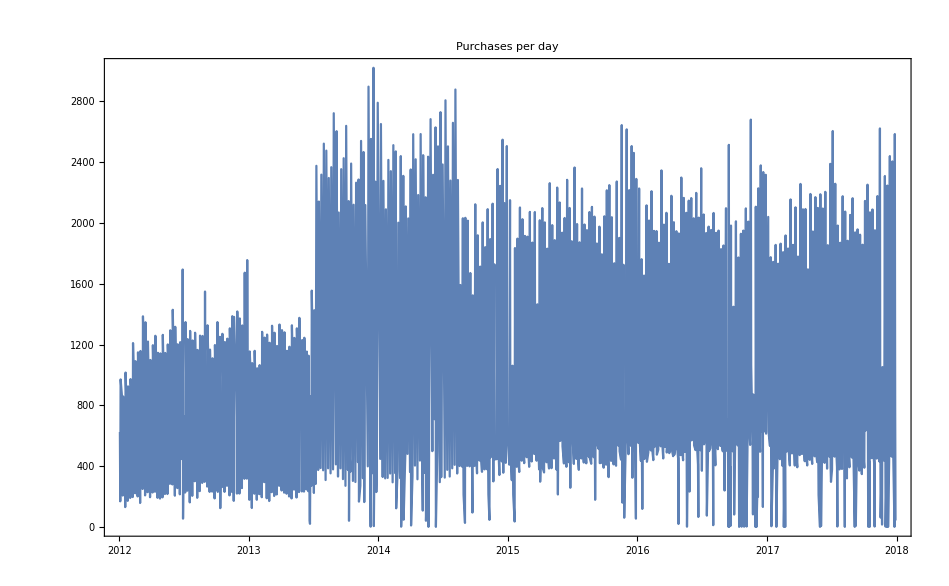

```mathematica
DateListPlot[invoice[Counts,"Date"],PlotLabel->"Purchases per day"]
```

The above is interesting, as it shows that something occurred around mid-2013 that shot sales per day up.

We can look at a moving average to see more general trends.

```mathematica
MovingAverage[Values[invoice[Counts,"Date"]]//Normal,5]
```

{5386/5,1078,849,3547/5,5821/5,3726/5,3619/5,584,4902/5,2988/5,887,4538/5,1022,3728/5,642,3772/5,4269/5,4226/5,5398/5,6071/5,4061/5,3577/5,728,3796/5,3043/5,3537/5,4976/5,5107/5,636,3767/5,5368/5,3968/5,648,3852/5,5272/5,3924/5,3914/5,6591/5,7043/5,5578/5,4913/5,4374/5,2566/5,1993/5,2467/5,477,4491/5,3903/5,3609/5,4819/5,1112,3948/5,6043/5,1294,987,865,1233,4761/5,4763/5,6387/5,6869/5,6574/5,1245,1226,5588/5,5567/5,3532/5,3287/5,4498/5,3106/5,598,4841/5,5091/5,3348/5,3394/5,4649/5,3279/5,3094/5,4957/5,1034,3841/5,5163/5,5307/5,3444/5,3237/5,567,589,2852/5,670,4747/5,5274/5,3761/5,5419/5,5406/5,4059/5,5387/5,1128,3889/5,3796/5,5414/5,4063/5,5184/5,5267/5,5347/5,5501/5,5478/5,836,5783/5,5903/5,4079/5,5689/5,5698/5,4013/5,1023,5249/5,3599/5,1060,5416/5,4136/5,5513/5,5642/5,3916/5,1113,1133,4148/5,5676/5,5781/5,3822/5,3308/5,1014,3604/5,5129/5,4924/5,5448/5,3877/5,3666/5,3776/5,4848/5,4707/5,5943/5,6107/5,4363/5,5674/5,1137,4128/5,784,6064/5,4276/5,4344/5,1261,6534/5,4323/5,745,1049,3531/5,3303/5,4779/5,5326/5,745,5357/5,5482/5,4108/5,3559/5,5252/5,3713/5,3529/5,4916/5,5457/5,755,5191/5,5449/5,4023/5,5644/5,5896/5,3844/5,5204/5,5244/5,3088/5,592,4917/5,3432/5,3306/5,5222/5,5358/5,3748/5,5152/5,5301/5,3768/5,1052,1109,4363/5,1219,6379/5,4236/5,4032/5,3358/5,3176/5,611,3506/5,5166/5,5703/5,4041/5,3491/5,998,3536/5,3448/5,5217/5,1189,885,6412/5,6633/5,4518/5,4199/5,3783/5,2213/5,1978/5,845,4689/5,935,805,718,3527/5,3544/5,3543/5,714,6009/5,4386/5,3956/5,1272,6674/5,4789/5,4167/5,6289/5,4664/5,3964/5,4034/5,4202/5,2588/5,2664/5,3152/5,2734/5,3424/5,3076/5,2929/5,2529/5,2838/5,599,3079/5,659,3336/5,3651/5,3251/5,547,2783/5,3384/5,550,2811/5,766,3079/5,2933/5,3561/5,795,2966/5,3421/5,3582/5,3906/5,718,3928/5,3913/5,3283/5,3292/5,3227/5,2938/5,3662/5,3712/5,3277/5,712,4657/5,4052/5,4073/5,3952/5,4179/5,3591/5,3006/5,3333/5,766,684,675,875,4046/5,3179/5,3124/5,3221/5,3283/5,3248/5,3569/5,3716/5,4051/5,693,692,3469/5,3709/5,3372/5,3394/5,3424/5,4007/5,612,703,3641/5,4058/5,3726/5,829,4082/5,3479/5,3457/5,3547/5,3217/5,662,3848/5,792,3337/5,4482/5,4129/5,4061/5,4654/5,4989/5,3766/5,3081/5,3048/5,2933/5,623,3514/5,3473/5,807,3279/5,3276/5,3424/5,4903/5,3742/5,4022/5,3804/5,4399/5,2932/5,728,3153/5,3283/5,3171/5,3106/5,601,3474/5,4058/5,685,3884/5,3427/5,705,3462/5,632,3327/5,880,4281/5,3708/5,4572/5,3976/5,3573/5,3122/5,3082/5,3176/5,3674/5,3412/5,3466/5,4109/5,3618/5,3579/5,3197/5,3031/5,2467/5,590,3848/5,3903/5,5127/5,4731/5,4203/5,785,4352/5,3499/5,3898/5,3441/5,3497/5,3392/5,3128/5,3364/5,853,738,3701/5,3703/5,3881/5,3379/5,631,2724/5,3688/5,2822/5,2862/5,3169/5,3244/5,2729/5,638,2716/5,2512/5,3466/5,3622/5,3188/5,3459/5,4067/5,3559/5,2929/5,3292/5,4097/5,3519/5,3041/5,3619/5,4372/5,3824/5,3751/5,3692/5,4288/5,3626/5,3754/5,3386/5,4632/5,790,3859/5,3192/5,4344/5,736,3236/5,3488/5,4594/5,4207/5,754,877,5172/5,915,868,4341/5,5226/5,4548/5,921,4034/5,4871/5,4053/5,746,3069/5,3968/5,3513/5,2794/5,2667/5,3701/5,3376/5,571,3298/5,3797/5,3366/5,2829/5,3279/5,3682/5,3339/5,2807/5,3326/5,3981/5,3646/5,648,3677/5,3813/5,755,3692/5,3586/5,4219/5,800,585,2958/5,3981/5,3466/5,3043/5,3521/5,833,3763/5,3216/5,3586/5,843,726,3034/5,3364/5,3659/5,3572/5,3104/5,3469/5,4267/5,4134/5,3183/5,3511/5,4227/5,3819/5,3284/5,865,858,3809/5,3104/5,3393/5,3271/5,3531/5,2918/5,3176/5,3847/5,3569/5,2933/5,3422/5,4272/5,4013/5,3378/5,3791/5,869,3846/5,3113/5,3362/5,4068/5,737,3087/5,3442/5,4323/5,3768/5,4137/5,4554/5,4239/5,3474/5,3184/5,3199/5,557,711,3191/5,663,3224/5,3518/5,2856/5,569,3386/5,455,2608/5,2537/5,3856/5,550,680,701,932,3329/5,3927/5,1122,4928/5,3877/5,4137/5,5836/5,5601/5,5706/5,5704/5,7742/5,1580,6068/5,7976/5,7989/5,7834/5,5711/5,7522/5,1121,1150,1221,7896/5,8167/5,8163/5,10236/5,7926/5,6114/5,5792/5,7771/5,5553/5,7567/5,1510,5752/5,6037/5,5692/5,726,3618/5,3643/5,3269/5,5514/5,5577/5,5441/5,1537,5692/5,3727/5,5767/5,5764/5,5342/5,5469/5,1609,1116,7969/5,6221/5,8843/5,1260,1714,6268/5,5904/5,3113/5,1110,3607/5,6007/5,6449/5,8496/5,6034/5,1205,5464/5,5339/5,5477/5,7489/5,7521/5,7943/5,7914/5,5854/5,5984/5,1151,3611/5,3639/5,5286/5,969,7032/5,8773/5,10891/5,8891/5,7172/5,982,642,252,722,756,4094/5,739,3539/5,3771/5,5709/5,5751/5,1585,1581,5758/5,5924/5,5628/5,3732/5,5864/5,7596/5,5367/5,1060,7448/5,5353/5,637,5512/5,5572/5,5453/5,5601/5,8229/5,1251,8658/5,6342/5,6343/5,6443/5,6029/5,1182,6237/5,6062/5,1228,8349/5,1268,6344/5,8298/5,5877/5,6032/5,8534/5,8611/5,6684/5,8581/5,6323/5,5037/5,5484/5,5529/5,5277/5,1098,5932/5,5289/5,5424/5,684,4821/5,3189/5,4647/5,4584/5,4956/5,3417/5,4539/5,3263/5,2889/5,599,4642/5,704,3688/5,3946/5,1072,742,5021/5,979,5037/5,5122/5,5012/5,3858/5,760,5146/5,731,5383/5,5204/5,6719/5,5367/5,5069/5,605,4772/5,3336/5,3327/5,3672/5,785,3526/5,3513/5,5388/5,1055,5581/5,6097/5,5994/5,4279/5,4263/5,1241,4562/5,6351/5,6068/5,8143/5,6213/5,6246/5,4537/5,918,4234/5,4123/5,4131/5,4017/5,4668/5,2998/5,4326/5,3896/5,3624/5,602,4427/5,2988/5,3266/5,3592/5,5247/5,3799/5,3839/5,5374/5,5542/5,1070,5321/5,1360,5546/5,1095,4132/5,5583/5,4064/5,5366/5,5482/5,5346/5,4021/5,5697/5,821,4057/5,4062/5,4981/5,3579/5,5116/5,4968/5,966,4023/5,5451/5,3824/5,3804/5,1102,6683/5,5101/5,5136/5,5263/5,5521/5,815,1109,5722/5,5623/5,3877/5,5379/5,3844/5,3839/5,1137,5547/5,3874/5,4038/5,1115,3918/5,4106/5,5828/5,5744/5,5642/5,5484/5,5457/5,1161,1134,4063/5,4291/5,5851/5,4196/5,843,4047/5,5281/5,3851/5,5587/5,5848/5,6038/5,6151/5,5989/5,5497/5,5197/5,1040,5434/5,5483/5,4034/5,4232/5,5771/5,4127/5,5524/5,5519/5,5477/5,5559/5,5438/5,5591/5,5624/5,5508/5,779,3981/5,3917/5,4109/5,4197/5,5987/5,7304/5,5441/5,5342/5,5351/5,5078/5,3633/5,3876/5,1025,1030,5218/5,5188/5,5362/5,5783/5,1131,4191/5,4129/5,5571/5,3791/5,3872/5,5027/5,5111/5,3511/5,5349/5,5438/5,4106/5,5596/5,5692/5,3917/5,5981/5,6184/5,945,5916/5,5997/5,3513/5,3531/5,3149/5,427,4172/5,6228/5,6211/5,6629/5,8424/5,6342/5,4858/5,915,6557/5,950,6506/5,6238/5,5969/5,4101/5,791,3892/5,4019/5,5726/5,5569/5,5451/5,3343/5,4406/5,3091/5,3351/5,5032/5,5342/5,4179/5,5748/5,5679/5,5772/5,5847/5,5892/5,4316/5,5637/5,3954/5,3991/5,5402/5,5438/5,1072,5416/5,5383/5,5782/5,5837/5,4568/5,1195,5994/5,4099/5,5747/5,5674/5,5752/5,1143,1399,5412/5,1074,3814/5,3856/5,826,813,809,4008/5,5422/5,3973/5,5373/5,5357/5,5473/5,3547/5,1058,3832/5,3926/5,5501/5,1184,823,4137/5,1132,4029/5,5737/5,1175,5382/5,3874/5,3573/5,718,3602/5,834,5642/5,5946/5,1196,5842/5,5868/5,5872/5,5746/5,825,737,3594/5,3919/5,4179/5,3972/5,5962/5,6001/5,4268/5,5531/5,5754/5,3773/5,1041,5028/5,3593/5,3519/5,5398/5,4031/5,5647/5,1158,5797/5,771,3652/5,3521/5,3554/5,3654/5,5592/5,5698/5,4296/5,4173/5,1075}

```mathematica
(Keys[invoice[Counts,"Date"]]//Normal)[[5;;]]//Length
```

1017

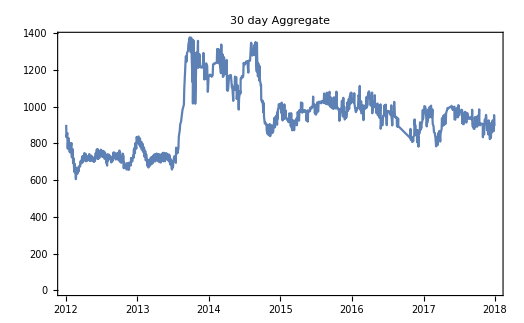

```mathematica
DateListPlot[Association[Thread[(Keys[invoice[Counts,"Date"]]//Normal)[[30;;]]->MovingAverage[Values[invoice[Counts,"Date"]]//Normal,30]]],PlotLabel->"30 day Aggregate"]
```

Let us check the type of objects we have

```mathematica
Head/@invoice[[1]]
```

```mathematica
Keys[Head/@invoice[[1]]]//Normal
```

{Invoice_id,Date,Item_id,Vendor_id,Vendor_Name,Store_id,Store_Name,Address,City_Name,Zip_Code,County_id,County_Name,Bottles_Sold}

```mathematica
invoice[Counts,#]&/@{"Date","Item_id","Vendor_id","Vendor_Name","Store_id","Store_Name","Address","City_Name","Zip_Code","County_id","County_Name","Bottles_Sold"}
```

{,,,,,,,,,,,}

There seems to be one unsold item

```mathematica
{(invoice[Counts, "Item_id"]//Length) ,(item//Length)}
```

{4165,4166}

```mathematica
Complement[Normal[item[All,"Item_id"]],invoice[All, "Item_id"]//Normal//Union]
```

{103}

```mathematica
Select[item,#["Item_id"]==103&]
```

In terms of pure numerical interesting raw data that would be the Bottles Sold, as the rest is mostly identifiers we will work on information about specific identifiers later

```mathematica
invoice[Counts,"Bottles_Sold",Head]
```

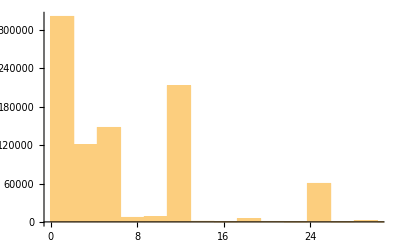

```mathematica
invoice[Histogram,"Bottles_Sold"]
```

If wanted we can adjust the bin counts

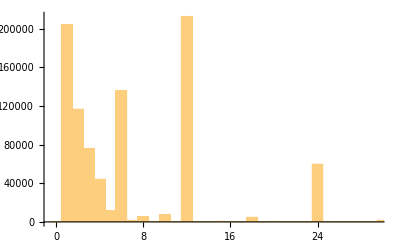

```mathematica
Histogram[invoice[All,"Bottles_Sold"],PlotRange->All]
```

```mathematica
Manipulate[Histogram[invoice[Select[#,#>n&]&,"Bottles_Sold"]],{n,0,1200,100}]
```

The good thing is that it is all integer data, so we can calculate Mean, Standard deviation, min and max

```mathematica
invoice[#,"Bottles_Sold",N]&/@{Mean,StandardDeviation,Min,Max}
```

{9.87565,22.4892,0.,2160.}

0 bottles sold is strange, so let us check those specific invoices

```mathematica
Select[invoice,#["Bottles_Sold"]==0&]//Length
```

73

```mathematica
Select[invoice,#["Bottles_Sold"]==0&]
```

```mathematica
Select[invoice,#["Bottles_Sold"]==2160&]
```

```mathematica
Select[withPurchaseCost,#["Bottles_Sold"]==2160&]
```

We can quickly see which ones were the ones with the lowest number of sales and the largest

```mathematica
Sort[invoice[Counts,"Store_Name"]]
```

Let us check the sales at the Artisan Craft Soda store

```mathematica
Select[invoice,#["Store_Name"]=="Artisan Craft Soda"&]
```

```mathematica
Select[itemInvoice,#["Store_Name"]=="Artisan Craft Soda"&]
```

Let us go back to the invoice data

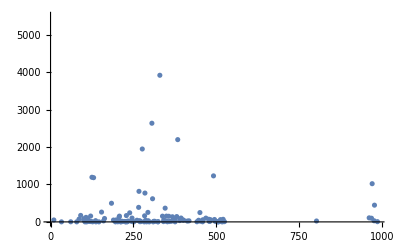

```mathematica
ListPlot[invoice[Counts,"Vendor_id"]]
```

It seems like most of the vendors are under the 4000 count in sales

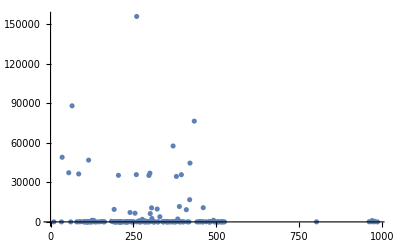

```mathematica
ListPlot[invoice[Counts,"Vendor_id"],PlotRange->All]
```

Although a few of them are way past that number

```mathematica
Max[invoice[Counts,"Vendor_id"]]
```

156106

```mathematica
Select[invoice[Counts,"Vendor_id"]//Normal,#==156106&]
```

<|260→156106|>

```mathematica
invoice[Select[#,#["Vendor_id"]==260&]&]
```

Dataset[<>]

Inuyasha brands having the biggest number of sales

```mathematica
item[[2000,1]]
```

43034

### Item

Let’s look at the data we could work with

```mathematica
Head/@item[[1]]
```

we can look at the different possible pack numbers

```mathematica
KeySort[item[Counts,"Pack"]]
```

Different Categories

```mathematica
Sort[item[Counts,"Category"]]
```

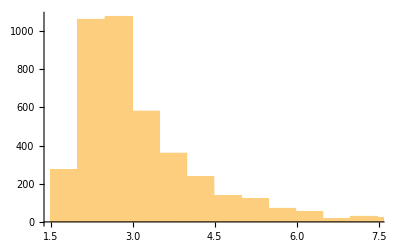

```mathematica
item[Histogram,"Bottle_Cost"]
```

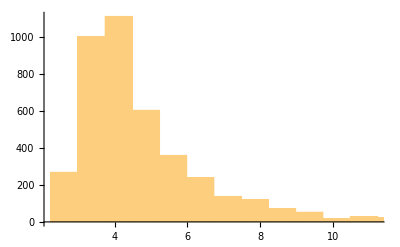

```mathematica
item[Histogram,"Bottle_Retail_Price"]
```

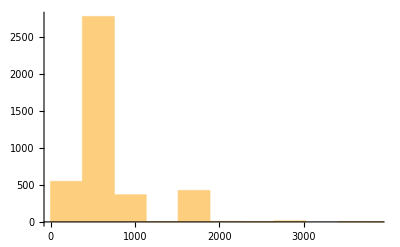

```mathematica
item[Histogram,"Bottle_Volume_ml"]
```

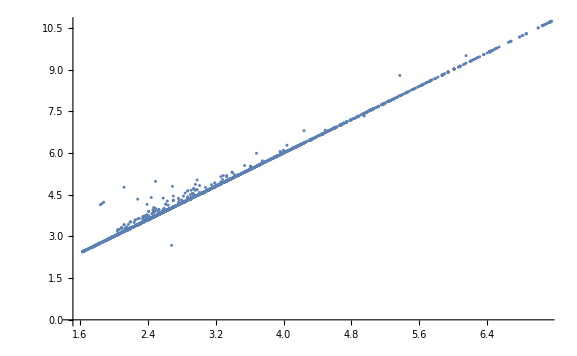

```mathematica
item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]
```

```mathematica
item[Max,"Bottle_Volume_ml"]
```

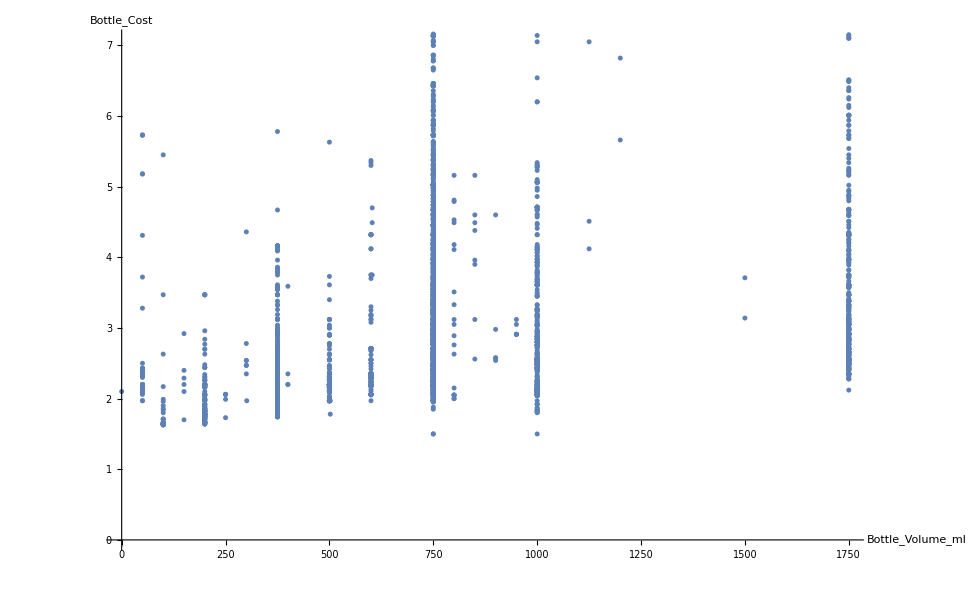

```mathematica
ListPlot[item[All,{"Bottle_Volume_ml","Bottle_Cost"}],AxesLabel->Automatic]
```

We can plot the whole spectrum

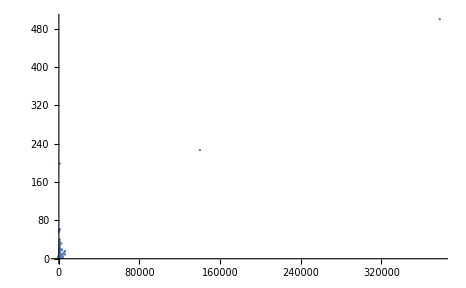

```mathematica
ListPlot[item[All,{"Bottle_Volume_ml","Bottle_Cost"}],PlotRange->All]
```

But we really loose interesting information

```mathematica
data=item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values;
```

```mathematica
LinearModelFit[item[All,{"Bottle_Cost","Bottle_Retail_Price"}]//Normal//Values,{1,x},x]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{4.32,6.48},{3.33,5.},{10.3,20.1},{4.44,6.66},{3.12,4.68},{3.92,5.88},{3.62,5.43},{2.77,4.16},{2.77,4.16},{2.77,4.16},{2.84,4.26},{3.48,5.22},{2.91,4.36},{4.32,6.48},{2.98,4.47},{2.54,3.81},{3.69,5.54},{3.96,5.94},4130,{2.16,3.24},{9.48,14.22},{3.94,5.91},{500.,750.},{2.35,3.53},{3.58,5.37},{3.86,5.79},{8.55,12.82},{9.,13.5},{40.25,60.38},{3.54,5.31},{19.99,29.99},{6.08,9.12},{12.6,18.9},{4.27,6.41},{5.87,8.81},{3.72,5.58},{6.81,10.22}},{1,x},x]
 |  |  |  |

```mathematica
Counts[Map[Head,data,{2}]]
```

<|{Real,Real}→4163,{Real,String}→3|>

```mathematica
DeleteCases[data,{_Real,_String}]
```

```mathematica
Counts[Map[Head,DeleteCases[data,{_Real,_String}],{2}]]
```

<|{Real,Real}→4163|>

```mathematica
model=LinearModelFit[DeleteCases[data,{_Real,_String}],{1,x},x]
```

FittedModel[0.0104165+1.49998 x]

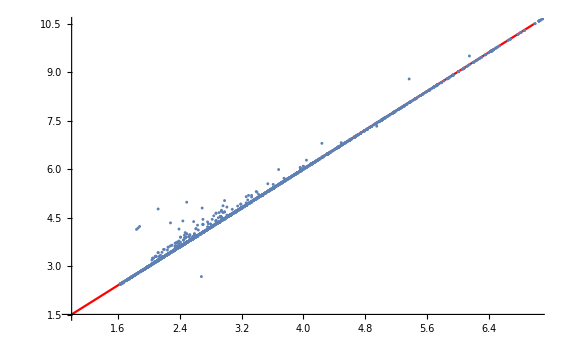

```mathematica
Show[Plot[model[x],{x,1,7},PlotStyle->Red],item[ListPlot,{"Bottle_Cost","Bottle_Retail_Price"}]]
```

```mathematica
Position[data,{_Real,_String}]
```

{{2176},{2355},{2475}}

```mathematica
item[[{2176,2355,2475}]]
```

```mathematica
Position[item[All,"Category"],""]
```

{{3},{3603},{3604},{3605}}

```mathematica
#["Item_Description"]&/@item[[{3,3603,3604,3605}]]
```

```mathematica
Normal@%
```

{Yummy Surstromming Juice,Miku's Leek Juice,Dark Fantasy,Butterbeer}

```mathematica
item[Counts,"Category"]
```

```mathematica
Length[item]
```

4166

```mathematica
item[[19]]
```

```mathematica
item[Union,"Item_Description"]//Length
```

4166

```mathematica
Length[item]
```

4166

```mathematica
RandomChoice[review,10]
```

```mathematica
review[Counts,"Customer_id"]
```

```mathematica
RandomChoice[review]/.x_Association:>Association[x,"Rating"->ToExpression[x["Product_Rating"]]*5 ]
```

We can do the above to the whole mixed Dataset (takes a few seconds)

```mathematica
withRating=(itemInvoice/.x_Association:>Association[x,"Purchase_Cost"->x["Bottle_Retail_Price"] x["Bottles_Sold"]]);
```

## Observations

The cost price relationship is roughly linear as  price ~ 0.0104165+1.49998 Cost

There are 12 different categories of drink and some are not labeled into a category (Yummy Surstromming Juice, Miku’s Leek Juice, Dark Fantasy, Butterbeer)